```mathematica
Needs["HierarchicalClustering`"]
```

The Duffing oscillator equation is solved as an initial value problem.  It depicts a damped oscillator (y’’[t]+y’[t]+y[t]) with a non-linearity (ϵ (y[t])^3).  The magnitude of ϵ has an effect on altering its temporal evolution.

With ϵ=0 (which we call “duffing0”), we recover dynamics of a linear damped oscillator  (think a damped pendulum).  This is plotted below in figure 1.  Forcing is excluded (γ=0) and damping is included (δ=1).

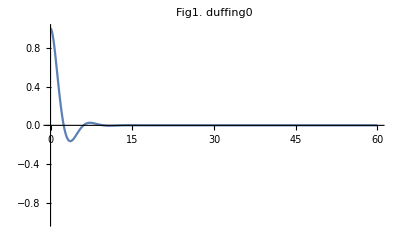

```mathematica
Module[{tmax=60,ϵ=0,δ=1,γ=0/10},
duffing0=NDSolveValue[{y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[duffing0[t],{t,0.,tmax},PlotLabel->"Fig1. duffing0",PlotRange->{{0,tmax},{-1,1}}]]
```

Next the Duffing oscillator has its non - linearity switched ON by introducing ϵ = 1.0.  This situation is now called “duffing1”.  The temporal dynamics are solved and plotted along with duffing0 in figure 2.

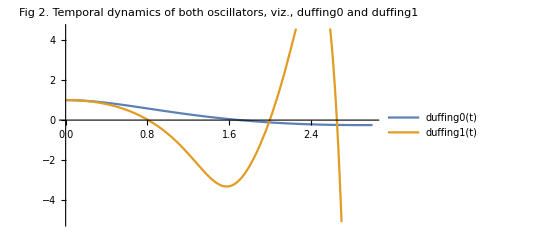

```mathematica
Module[{tmax=3,ϵ,δ=1,γ=0},
ϵ=0;
duffing0=NDSolveValue[{y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=1;
duffing0=NDSolveValue[{y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[{duffing0[t],duffing1[t](*,1/32(Cos[3 t] - Cos[t])-3/8 t Sin[t]*)},{t,0,tmax},PlotLegends->"Expressions",PlotLabel->"Fig 2. Temporal dynamics of both oscillators, viz., duffing0 and duffing1"]
]
```

Long time dynamics of the Duffing oscillator depicts a convergence of both duffing0 and duffing1 in figure 3.

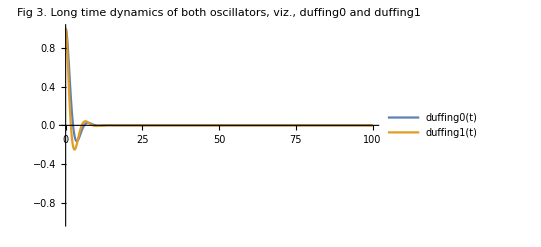

```mathematica
Module[{tmax=100,ϵ},
ϵ=0;
duffing0=NDSolveValue[{y''[t]+y'[t]+y[t]+ϵ (y[t])^3==0,y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=1.0;
duffing1=NDSolveValue[{y''[t]+y'[t]+y[t]+ϵ (y[t])^3==0,y[0]==1,y'[0]==0},y,{t,0,tmax},Method->"LSODA"];
Plot[{duffing0[t],duffing1[t](*,1/32(Cos[3 t] - Cos[t])-3/8 t Sin[t]*)},{t,0,tmax},PlotLegends->"Expressions",PlotLabel->"Fig 3. Long time dynamics of both oscillators, viz., duffing0 and duffing1",PlotRange->{{0,tmax},{-1,1}}]
]
```

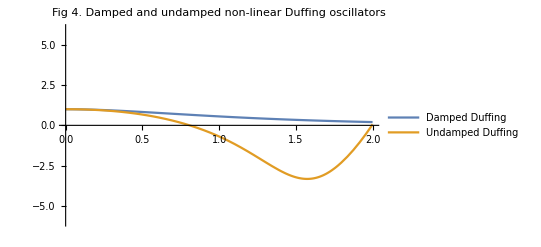

```mathematica
Module[{tmax=2,ϵ=1,a,stepSize=0.2,end=tmax},
a=2;
duffingD=NDSolveValue[{y''[t]+a y'[t]+y[t]+ϵ (y[t])^3==0,y[0]==1,y'[0]==0},y,{t,0,tmax}];
a=-2;
duffingU=NDSolveValue[{y''[t]+a y'[t]+y[t]+ϵ (y[t])^3==0,y[0]==1,y'[0]==0},y,{t,0,tmax},Method->"LSODA"];
Plot[{duffingD[t],duffingU[t](*,1/32(Cos[3 t] - Cos[t])-3/8 t Sin[t]*)},{t,0,tmax},PlotLegends->{"Damped Duffing","Undamped Duffing"},PlotLabel->"Fig 4. Damped and undamped non-linear Duffing oscillators",PlotRange->{{0,tmax},{-6,6}}]
]
```

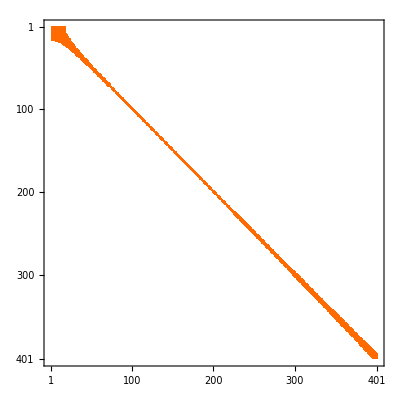

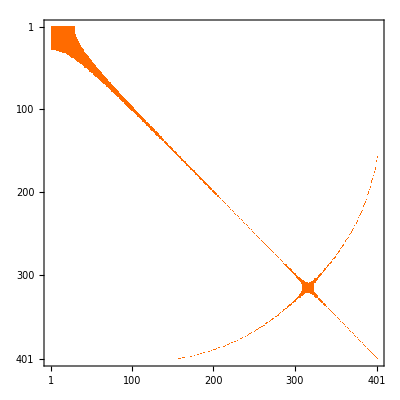

```mathematica
a=2;
ϵ=1.0;
tmax=2;
duffingD=NDSolveValue[{y''[t]+a y'[t]+y[t]+ϵ (y[t])^3==0,y[0]==1,y'[0]==0},y,{t,0,tmax}];
With[{stepSize=0.005,end=tmax},MatrixPlot[UnitStep[0.00005-DistanceMatrix[duffingD[Range[0,end,stepSize]]]]]]

a=-2;
ϵ=1.0;
duffingU=NDSolveValue[{y''[t]+a y'[t]+y[t]+ϵ (y[t])^3==0,y[0]==1,y'[0]==0},y,{t,0,tmax},Method->"LSODA"];
With[{stepSize=0.005,end=tmax},MatrixPlot[UnitStep[0.0005-DistanceMatrix[duffingU[Range[0,end,stepSize]]]]]]
```